# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 07 — Wednesday October 20, 2020

## Option Strategies, Model Extensions, Return Distributions, Optimal Growth, Portfolio Dynamics

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Options Strategies

Options are used extensively to control risk, make bets on complex market situations, and accomplish other trades that may not be otherwise achievable. Such actions are typically made building up the desired behavior by combining simpler instruments together. There are a number of standard strategies that have been developed.

### Basic Tools

We can construct a number of different trading strategies using the basic tools of a long or short position in the underling and buying or writing puts and calls on that underlying.  We’ll also build more complex strategies by combining simpler ones.

These strategies will be illustrated using net profit plots in the price of the underlying is plotted against the profit or loss of the total position at expiration. At this stage we won’t consider the effects of transaction costs or the impact of unwinding these positions before expiration.

We’ll assume that a position is put on at time t = 0 and evaluated at t = T when the options expire. The price of a stock, put and call is S(t), P(t) and C(t), respectively. Where we need to indicate different strikes, we’ll use subscripts; e.g., C_i(t) strike will be K_i.

The net profit of a long stock position is S(T) – S(0):

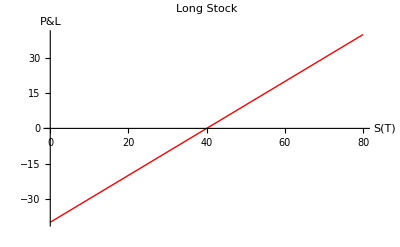

```mathematica
Plot[s-40,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Stock",PlotStyle->{Red,Thick}]
```

The net profit of a short stock position is S(0) – S(T):

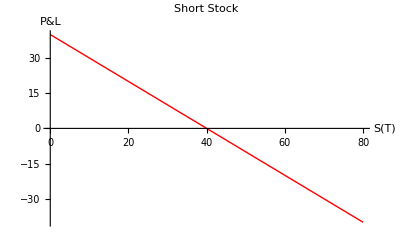

```mathematica
Plot[40-s,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Stock",PlotStyle->{Red,Thick}]
```

The net profit of a long call is Max[S(T) – K, 0] – C(0):

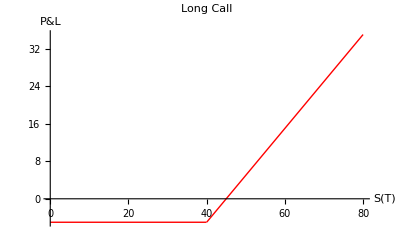

```mathematica
Plot[Max[s-40,0]-5,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Call",PlotStyle->{Red,Thick}]
```

The net profit of a short call is –Max[S(T) – K, 0] + C(0):

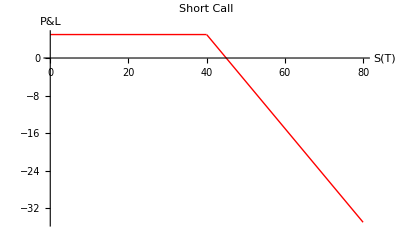

```mathematica
Plot[-Max[s-40,0]+5,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Call",PlotStyle->{Red,Thick}]
```

The net profit of a long put is Max[K – S(T) , 0] – P(0):

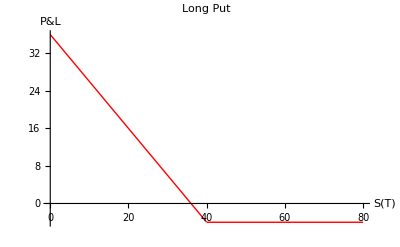

```mathematica
Plot[Max[40-s,0]-4,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Put",PlotStyle->{Red,Thick}]
```

The net profit of a short put is –Max[K – S(T) , 0] + P(0):

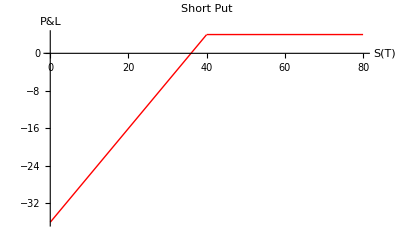

```mathematica
Plot[-Max[40-s,0]+4,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Put",PlotStyle->{Red,Thick}]
```

### Downside Protection

Investment involves risk. Sometimes the potential size of a loss associated with a position is unacceptable. A natural case in point is a short position in a stock. If you buy a share of stock for $50, then your maximum loss is your original $50 investment. On the other hand if you short that share of stock, then your potential loss is infinite.

Often the distressed securities that we short are also the most volatile. A $5 tech stock we are convinced is on its way out may suddenly announce a major contract and triple in price.

One way to control the downside risk of a stock is to buy an out-of-the-money call. The further out of the money the call is the lower the premium we will pay, but the further out our downside protection is. This makes sense: the more insurance we have, the more we have to pay for it.

We assume that the current price of the stock  S(0) = 40 and we buy a call at a strike of K = 50 with a premium C(0) = 2.

The net profits at expiration T of the two components of this strategy are plotted below. We’ve bought an option that’s out of the money to keep costs low. Thus, we have protected ourselves from catastrophic loses, but left ourselves exposed to some increases in stock price.

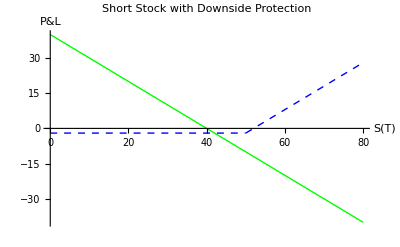

```mathematica
Show[
Plot[Max[s-50,0]-2,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Stock with Downside Protection",PlotStyle->{Blue,Thick,Dashed,Thick}],
Plot[40-s,{s,0,80},PlotStyle->{Green,Thick}],
PlotRange->All
]
```

Taken together they have the desired effect. Note, however, that the premium of the option costs us: the net profit line of the hedged position is slightly lower for prices below the strike price of the option.

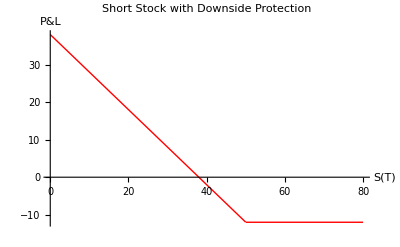

```mathematica
Plot[(Max[s-50,0]-2)+(40-s),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Stock with Downside Protection",PlotStyle->{Red,Thick}]
```

A similar strategy can be applied to a long position by offsetting it with a long put. Although we don’t face the prospect of unlimited loses, an investor might want to take advantage of the expected superior return on a stock, but may have future uses for the capital that requires that he or she place a floor on losses.

### Covered Call

A covered call is a hedged position in which an at-the-money call is written against a long position in the underlying. The the case below we have S(0) = 40, C(0) = 5 with K = 40.

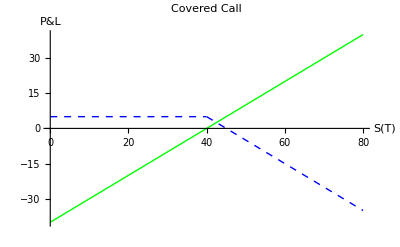

```mathematica
Show[
Plot[-Max[s-40,0]+5,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Covered Call",PlotStyle->{Blue,Thick,Dashed,Thick}],
Plot[s-40,{s,0,80},PlotStyle->{Green,Thick}],
PlotRange->All
]
```

We exchanged the upside potential of the stock in return for the premium on the call. A fund manager might want to do this if he or she were convinced that a stock is likely to hold to its current value or decrease only slightly.

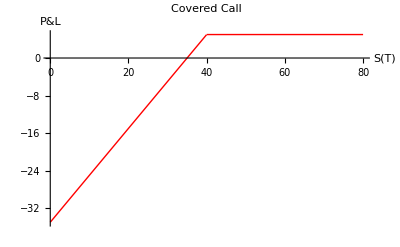

```mathematica
Plot[(-Max[s-40,0]+5)+(s-40),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Covered Call",PlotStyle->{Red,Thick}]
```

### Straddles and Strangles

Sometimes we are convinced that a stock will not move much. It may be in a stable business and an investor’s assessment of economic conditions is that there is little that is likely to come along to change things. On the other hand an investor may be convinced that a stock’s price will be highly volatile, but isn’t sure if it will go up or down. An example would a company awaiting the resolution of a lawsuit; if the company wins the price will increase dramatically, but if it loses the price will plummet.

#### Straddles

A long straddle is a long call and a long put on the same underlying, both bought at the money. Here we have S(0) = 40, P(0) = 4, C(0) = 5:

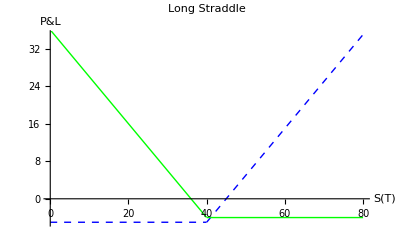

```mathematica
Show[
Plot[Max[s-40,0]-5,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Straddle",PlotStyle->{Blue,Thick,Dashed}],
Plot[Max[40-s,0]-4,{s,0,80},PlotStyle->{Green,Thick}]
]
```

Clearly, this strategy makes sense if the investor expects the stock to move dramatically but isn’t sure what direction it will move.

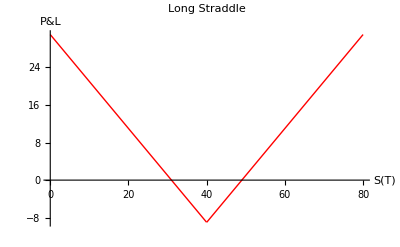

```mathematica
Plot[(Max[s-40,0]-5)+(Max[40-s,0]-4),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Straddle",PlotStyle->{Red,Thick}]
```

A short straddle simply reverses the trades.

#### Strangles

By buying the put and call at different strike prices it’s possible to implement a similar strategy called a strangle. This is a bit cheaper to implement but doesn't “kick in” unless the movement of the price is above some threshold.

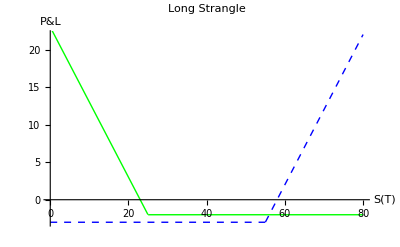

```mathematica
Show[
Plot[Max[s-55,0]-3,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Strangle",PlotStyle->{Blue,Thick,Dashed}],
Plot[Max[25-s,0]-2,{s,0,80},PlotStyle->{Green,Thick}]
]
```

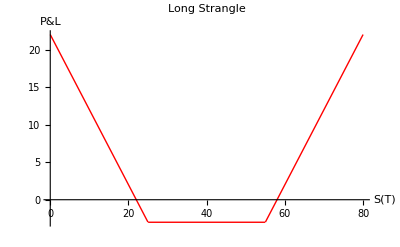

```mathematica
Plot[(Max[s-55,0]-2)+(Max[25-s,0]-1),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Strangle",PlotStyle->{Red,Thick}]
```

A short strangle simply reverses the trades.

### Butterflies to Control the Downside

Once we begin to build a “library” of hedge strategies we can think of combining them to produce more complex results. For example, consider the net profit plot for a short straddle:

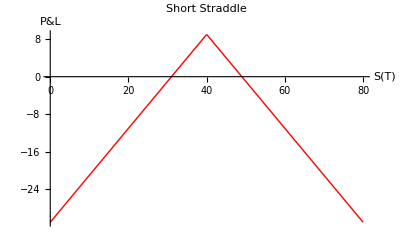

```mathematica
Plot[(-Max[s-40,0]+5)+(-Max[40-s,0]+4),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Short Straddle",PlotStyle->{Red,Thick}]
```

While an investor may have an opinion that a stock’s price will not change dramatically, he or she may hold that opinion with varying levels of confidence. A short straddle exposes it holder to very limited upside compared to potentially huge downside.

One way to control this risk is to put on a long strangle on top of the short straddle. The strangle’s strikes are in the money and its premiums are, therefore, less than those of the straddle whose strikes are at the money. The long straddle looks like:

```mathematica
Plot[(Max[s-55,0]-2)+(Max[25-s,0]-1),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Strangle",PlotStyle->{Red,Thick}]
```

-Graphics-

Putting them together produces what is called a long butterfly:

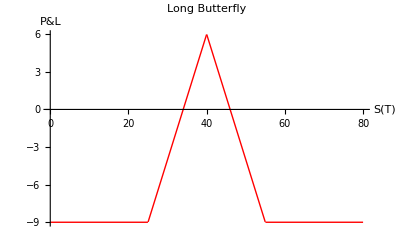

```mathematica
Plot[(-Max[s-40,0]+5)+(-Max[40-s,0]+4)+(Max[s-55,0]-2)+(Max[25-s,0]-1),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Long Butterfly",PlotStyle->{Red,Thick}]
```

Viewing a butterfly as a combination of a straddle and strangle is far easier to visualize than viewing it in terms of its simplest components. A short butterfly simply reverses the positions.

## Synthetic Positions

Synthetic positions, a portfolio of options whose pay-offs replicate those of the underlying, have many applications. Some stocks are difficult to short, so a synthetic short is a more practical was to take a short position than a “real” short. There are cases in which it would be illegal or not politic to sell a stock position; a synthetic short could accomplish the same thing. Investors frequently employ leverage to magnify returns. Often a suitable options position is the best way to achieve this leverage.

### Straight Synthetic Positions

A synthetic long is achieved by writing a put and buying a call, both usually (but not always) at the money:

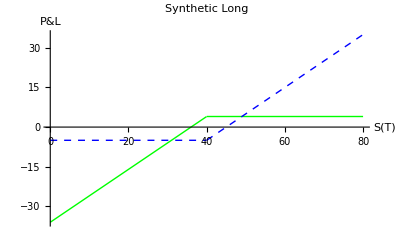

```mathematica
Show[
Plot[-Max[40-s,0]+4,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Synthetic Long",PlotStyle->{Green,Thick}],
Plot[Max[s-40,0]-5,{s,0,80},PlotStyle->{Blue,Thick,Dashed}],
PlotRange->All
]
```

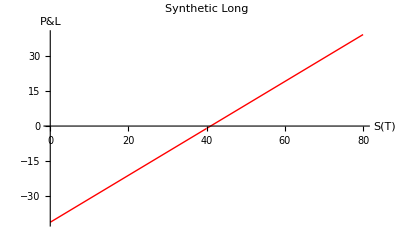

```mathematica
Plot[(-Max[40-s,0]+4)+(Max[s-40,0]-5),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Synthetic Long",PlotStyle->{Red,Thick}]
```

Note that the synthetic long does not exactly reproduce the profit and loss of the underlying but it comes close.

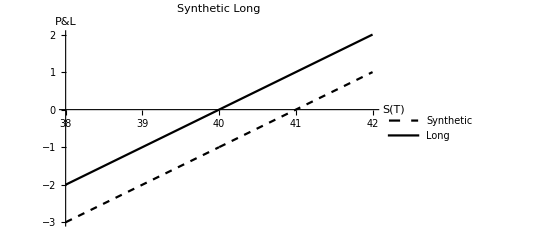

```mathematica
Show[
Plot[(-Max[40-s,0]+4)+(Max[s-40,0]-5),{s,38,42},AxesLabel->{"S(T)","P&L"},PlotLabel->"Synthetic Long",PlotStyle->{Black,Dashed},PlotLegends->LineLegend[{{Black,Dashed},Black},{"Synthetic","Long"}]],
Plot[s-40,{s,38,42},PlotStyle->Black],
PlotRange->All
]
```

Reversing the positions produces a synthetic short.

### Boxes

A box can be thought of two offsetting synthetic positions, one long and one short. The options in the long component are written at a strike below the underlying’s and the options of the short component are written at one higher:

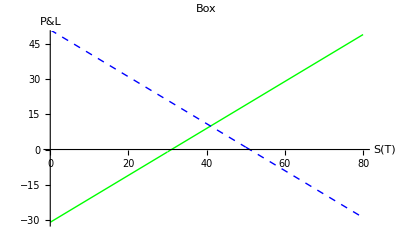

```mathematica
Show[
Plot[(-Max[30-s,0]+4)+(Max[s-30,0]-5),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Box",PlotStyle->{Green,Thick}],
Plot[(Max[50-s,0]-4)+(-Max[s-50,0]+5),{s,0,80},PlotStyle->{Blue,Thick,Dashed}]
]
```

Again, it is easier to visualize a box as a combination of synthetic positions rather than in terms of the base options positions. The net effect is to lock in a profit, with no upside or downside participation:

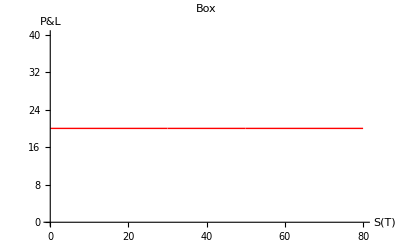

```mathematica
Plot[(-Max[30-s,0]+4)+(Max[s-30,0]-5)+(Max[50-s,0]-4)+(-Max[s-50,0]+5),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Box",PlotStyle->{Red,Thick},AxesOrigin->{0,0},PlotRange->{Automatic,{0,40}}]
```

## Vertical Spreads

Vertical spreads are means of producing synthetic positions with both up- and downside protection.

### Vertical Spread Using Calls

A long call sold at a strike below that of the underlying and a short call written at a strike above that of the underlying constructs bullish vertical spread.

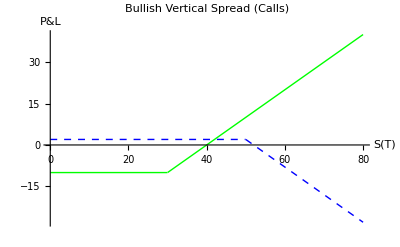

```mathematica
Show[
Plot[Max[s-30,0]-10,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Bullish Vertical Spread (Calls)",PlotStyle->{Green,Thick}],
Plot[-Max[s-50,0]+2,{s,0,80},PlotStyle->{Blue,Thick,Dashed}],
PlotRange->All
]
```

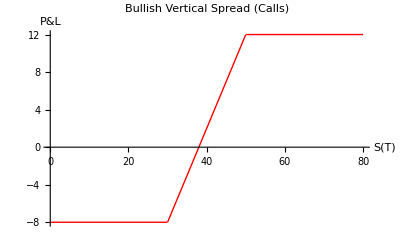

```mathematica
Plot[(Max[s-30,0]-10)+(-Max[s-50,0]+2),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Bullish Vertical Spread (Calls)",PlotStyle->{Red,Thick}]
```

A bearish vertical spread is achieved by reversing the positions of a bullish vertical spread, e.g.,

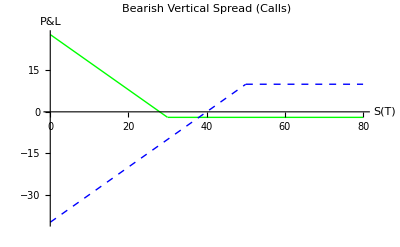

```mathematica
Show[
Plot[Max[30-s,0]-2,{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Bearish Vertical Spread (Calls)",PlotStyle->{Green,Thick}],
Plot[-Max[50-s,0]+10,{s,0,80},PlotStyle->{Blue,Thick,Dashed}],
PlotRange->All
]
```

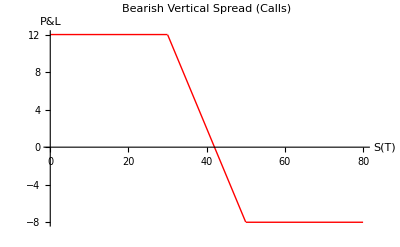

```mathematica
Plot[(-Max[30-s,0]+2)+(Max[50-s,0]-10),{s,0,80},AxesLabel->{"S(T)","P&L"},PlotLabel->"Bearish Vertical Spread (Calls)",PlotStyle->{Red,Thick}]
```

### Vertical Spreads Using Puts

Vertical spreads can also be constructed using puts. This is left as an exercise.

## Getting the Details Right

There’s still a lot of details to consider before anyone goes out and starts trading options.

### Transaction Costs

Trades are entered into to either increase return or decrease risk–often both. As such an investor needs to accurately balance costs against benefits in order to decide whether or not a given strategy makes sense. The transaction costs—both the fees paid and the bid-ask spreads in the market—are important elements that we haven’t explored here.

### Time Decay and the Potential for Early Exercise

We evaluated the net profit assuming the trade is entered into at time t = 0 and completed at time t = T. Unfortunately, events sometimes intervene. Some of the options may be subject to early exercise. Other financial pressures may arise that demand immediate capital. The point is that part of the assessment of the risk of a strategy has to factor in the time decay of its options:

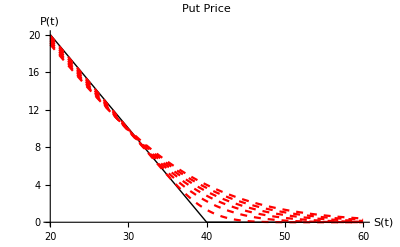

```mathematica
Show[
Plot[FinancialDerivative[{"European","Put"},{"StrikePrice"->40,"Expiration"->0.},{"CurrentPrice"->s,"Volatility"->0.3,"InterestRate"->0.03}],{s,20,60},AxesLabel->{"S(t)","P(t)"},PlotLabel->"Put Price",PlotStyle->{Black,Thick}],
Table[Plot[FinancialDerivative[{"European","Put"},{"StrikePrice"->40,"Expiration"->t},{"CurrentPrice"->s,"Volatility"->0.3,"InterestRate"->0.03}],{s,20,60},PlotStyle->{Red,Dashed}],{t,1/12,11/12,2/12}]
]
```

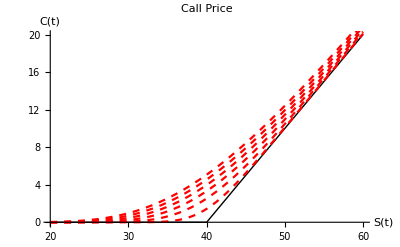

```mathematica
Show[
Plot[FinancialDerivative[{"European","Call"},{"StrikePrice"->40,"Expiration"->0.},{"CurrentPrice"->s,"Volatility"->0.3,"InterestRate"->0.03}],{s,20,60},AxesLabel->{"S(t)","C(t)"},PlotLabel->"Call Price",PlotStyle->{Black,Thick}],
Table[Plot[FinancialDerivative[{"European","Call"},{"StrikePrice"->40,"Expiration"->t},{"CurrentPrice"->s,"Volatility"->0.3,"InterestRate"->0.03}],{s,20,60},PlotStyle->{Red,Dashed}],{t,1/12,11/12,2/12}]
]
```

### Dividends and Other Distributions

Distributions, such as dividends, can materially affect the price of a stock. When a stock pays a dividend its price declines by a commensurate amount. Generally, the pricing function of an option is based on the raw price of the stock and does not take adjustments for dividends into account.

### More Complex Strategies

We’ve just scratched the surface of options strategies. For example, we haven’t consider strategies across different underlying securities, nor have we looked at strategies involving more than one expiration date. 

Wikipedia’s http://en.wikipedia.org/wiki/Option_strategies and its follow-on articles have a good overall write-ups. There are other strategies using options whose focus isn't necessarily pure risk control; e.g., volatility arbitrage (See http://en.wikipedia.org/wiki/Volatility_arbitrage.) is a form of statistical arbitrage in which trades buy volatility when it is judged to be underpriced and sell it when it is overpriced.

## More Complex Behaviors

The basic constant-coefficient geometric Itô process we have used so far to model asset returns makes some simplifying assumptions. More realistic models exist and these are an active area of research. We will examine two possible extensions: jump diffusion and stochastic volatility.

Under the assumptions of the simplest form of the Black-Scholes formula for European options that we have explored in this course, the stochastic process describing the price evolution of the underlying is a constant coefficient geometric Brownian motion; additionally, we assume that the risk-free rate is also constant. In practice we know this not to be true. Real securities prices have non-stationary drifts and volatilities and are also subject to discontinuous jumps.

### Jumps

We assume that we have an jump arrival rate 0<λ<1 and a time increment 0<Δ so that 0<λ Δ<<1 and can, therefore, approximate the jump process by a random variable indicator variable I(λ Δ)∈{0,1} which realizes a 1 with probability λ Δ and a 0 with probability 1-λ Δ. The distribution of a jump if it occurs is Normal[τ, ν].

Note that this approximation assumes that at most one jump will occur in an interval Δ. Clearly, if λ were, for example, the parameter of a Poisson process, then more than one jump can occur in any interval no matter how small. However, with Δ small enough then this probability will be negligible and can be ignored.

A geometric continuous-jump diffusion process can be created by extending our earlier binomial model. This can be used to model the return process of a financial asset.

Recall the standard binomial process over  t ϵ [0, 1] using n steps, each of length Δ = 1/n

B(t)=B(t-Δ)+X(t) √Δ

where the X(t) are i.i.d. random variables

X(t)={+1,   with prob.  1/2
-1,   with prob.  1/2

X(t)  is not observed until the end of the interval at  t. In other words, there is no lookahead to future random events. Let

ΔB(t)=B(t)-B(t-Δ)=X(t)√Δ

We then modeled the price dynamics of a financial asset using the geometric process

ΔS(t)=μ S(t)Δ+σ S(t) ΔB(t)

and further developed a continuous version by letting n→∞ (Δ→0)

ⅆS(t)=μ S(t)ⅆt+σ S(t) ⅆB(t)

Finally, we used these result to motivate the development of a process where we started with infinitesimal time increments, the Wiener process ⅆW(t), and used it to create the constant coefficient Itô process to model stock returns

ⅆS(t)=μ S(t)ⅆt+σ S(t) ⅆW(t)

In the same way we can extend the geometric model by adding a jump component with

ΔJ(t | λ,τ,ν)=N[τ, ν]I(λ Δ)

ΔS(t)=μ S(t)Δ+σ S(t) ΔB(t)+S(t) ΔJ(t | λ,τ,ν)

As we did before, we can continue the development by adding jumps and extend the geometric constant coefficient Itô process into the form

ⅆS(t)=μ S(t)ⅆt+σ S(t) ⅆW(t)+S(t)ⅆJ(t | λ,τ,ν)

where ⅆJ(t) is a standardized jump process in continuous time. As with the original Itô process the parameters can be functions of S(t) and t rather than constants.

### Stochastic Volatility

One element of the geometric constant coefficient Itô process that does not adequately model asset returns is the assumption that σ is constant over time. Stochastic volatility models treat volatility as a separate time dependent process σ(t) with its own set of dynamics.

A commonly used model for stochastic volatility is the Heston model. This is a model for the dynamics of the variance of the return (https://en.wikipedia.org/wiki/Heston_model). The price dynamics of the asset follow a geometric volatility √(ν(t))

ⅆS(t)=μ S(t)ⅆt+√(ν(t)) S(t) ⅆW_S(t)

with the variance ν(t) following

ⅆν(t)=κ(θ-ν(t))ⅆt+ξ √(ν(t))ⅆW_ν(t)

where ⅆW_S(t) and ⅆW_ν(t) are independent Wiener processes for the price and variance dynamics, respectively.

## Examining Daily Returns of the S&P 500 Index

An examination of the daily returns of the S&P 500 Index shows that the assumptions of a constant-coefficient geometric Itô process are clearly simplifications. We will first examine deviations from a Normal distribution and then look at how volatility changes over time.

We want to examine the actual daily log returns of the S&P 500 stock index. Using FinancialData[] we download data from 1960 to the current date, covert to log prices and compute returns by taking the first-order differences. We then plot the prices and returns.

```mathematica
mxSP500Index=FinancialData["^GSPC",{{1960,1,1},{2020,09,30}},Method->"Legacy"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"mxSP500Index.m"}],mxSP500Index]
```

/Volumes/Files/Programming/Foundations of Quantitative Finance/Lecture 7/mxSP500Index.m

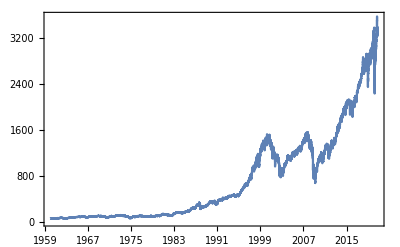

```mathematica
DateListPlot[mxSP500Index]
```

```mathematica
mxSP500LogIndex={First@#,Log@Last@#}&/@mxSP500Index;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"mxSP500LogIndex.m"}],mxSP500LogIndex]
```

/Volumes/Files/Programming/Foundations of Quantitative Finance/Lecture 7/mxSP500LogIndex.m

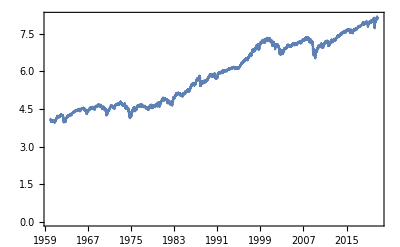

```mathematica
DateListPlot[mxSP500LogIndex]
```

```mathematica
mxSP500LogReturn=Transpose[{Rest[mxSP500LogIndex⟦All,1⟧],Differences[mxSP500LogIndex⟦All,2⟧]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"mxSP500LogReturn.m"}],mxSP500LogReturn]
```

/Volumes/Files/Programming/Foundations of Quantitative Finance/Lecture 7/mxSP500LogReturn.m

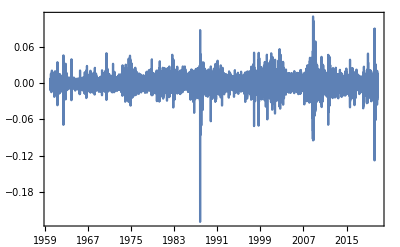

```mathematica
DateListPlot[mxSP500LogReturn,PlotRange->All]
```

```mathematica
distGaussian=EstimatedDistribution[mxSP500LogReturn⟦All,2⟧,NormalDistribution[m,s]]
```

NormalDistribution[0.000263406,0.0102886]

```mathematica
mxGaussian=Transpose[{mxSP500LogReturn⟦All,1⟧,RandomVariate[distGaussian,Length[mxSP500LogReturn⟦All,2⟧]]}];
```

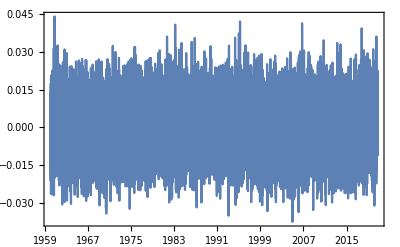

```mathematica
DateListPlot[mxGaussian,PlotRange->All]
```

As you can see from the log returns there are large deviations that appear inconsistent with a Normal distribution. We take the mean, standard deviation, skewness, and kurtosis of the returns. A Normal distribution has a skewness of 0 and kurtosis of 3. Kurtosis is a measure of how “fat” the tails of the distribution are.

```mathematica
Through[{Mean,StandardDeviation,Skewness,Kurtosis}[Last/@mxSP500LogReturn]]
```

{0.000263406,0.0102889,-1.03597,29.8231}

From the results above we see that not only is the log return distribution negatively skewed but has much fatter tails than a Normal. This means that not only are there more losses than gains but that log returns of large size relative to the standard deviation are more likely than a Normal. We can compare an empirical distribution of the log returns to a Normal.

```mathematica
distKernel=SmoothKernelDistribution[Last/@mxSP500LogReturn,"Oversmooth"];
```

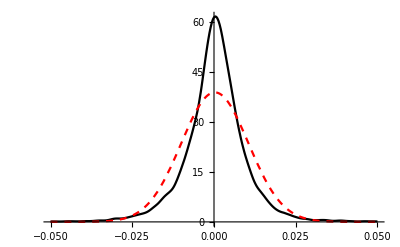

```mathematica
Plot[{PDF[distKernel,x],PDF[distGaussian,x]},{x,-0.05,0.05},PlotStyle->{{Black},{Red,Dashed}},PlotRange->All]
```

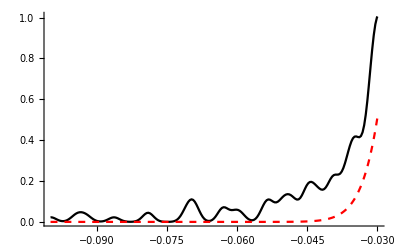

```mathematica
Plot[{PDF[distKernel,x],PDF[distGaussian,x]},{x,-0.10,-0.03},PlotStyle->{{Black},{Red,Dashed}},PlotRange->All]
```

```mathematica
distStudentT=EstimatedDistribution[Last/@mxSP500LogReturn,StudentTDistribution[m,s,d]]
```

StudentTDistribution[0.00046563,0.00621358,2.96381]

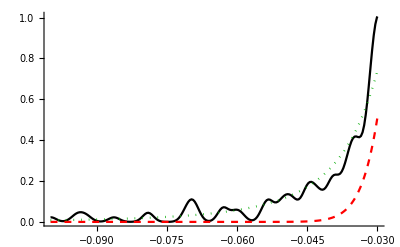

```mathematica
Plot[{PDF[distKernel,x],PDF[distGaussian,x],PDF[distStudentT,x]},{x,-0.10,-0.03},PlotStyle->{{Black},{Red,Dashed},{Darker[Green],Dotted}},PlotRange->All]
```

That may not seem like much of a difference but if we look at the difference in terms of a 99.9% VaR and CVaR:

VaR_(δ,χ)=-F_δ^-1[1-χ]

CVaR_(δ, χ)=E[ -r | r ≤ (–VaR)_(δ,χ)] =-1/(1-χ)∫_(-∞)^(-VaR_(δ, χ)) r ⅆF_δ[r]

The theoretical values based on the Normal distribution are:

```mathematica
nVaRGaussian=InverseCDF[distGaussian,1-0.999]
nCVaRGaussian=1/(1-0.999)∫_(-∞)^nVaRGaussian r PDF[distGaussian,r]ⅆr
```

-0.0315306

-0.0343791

The values based on a more realistic Student t distribution

```mathematica
nVaRStudentT=InverseCDF[distStudentT,1-0.999]
nCVaRStudentT=1/(1-0.999)NIntegrate[r PDF[distStudentT,r],{r,-∞,nVaRStudentT}]
```

-0.0641563

-0.0975978

Comparing these two results, the differences are startling.

```mathematica
Grid[{
{"S&P 500 Daily Log Return Risk Factors (χ = 0.999)"},{TableForm[100.{{nVaRGaussian,nCVaRGaussian},{nVaRStudentT,nCVaRStudentT}},TableHeadings->{{"Normal","Student"},{"VaR %","CVaR %"}}]}
},Frame->All]
```

S&P 500 Daily Log Return Risk Factors (χ = 0.999)
 | VaR % | CVaR %
Normal | -3.15306 | -3.43791
Student | -6.41563 | -9.75978

### Example — Local Volatility of the S&P 500 Index

For daily log returns σ^2[r]≃E[r^2], if we take the cumulative sum of the squared returns, then the slope of that line is a measure of variance.

σ^2[r]=𝔼[r^2]-𝔼[r]^2

In the case of daily returns we note that

𝔼[r^2]>>𝔼[r]^2

And a reasonable approximation of the variance is

σ^2[r]≃𝔼[r^2]

This motivates the following

σ_t^2[r]≃1/t∑_(i=1)^t (r(i))^2    ⟹    ∑_(i=1)^t (r(i))^2 ≃t σ^2

We can use this to develop insights into how the variability varies across time.

If the variance of returns were constant, then the plot below would be a straight line. Clearly, however, there are different regimes of higher and lower variability, including short intervals of explosive volatility. This is a very different picture from we would see with a constant variance distribution.

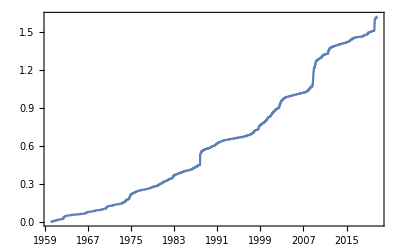

```mathematica
DateListPlot[{First/@#,Accumulate[(Last/@#)^2]}ᵀ&[mxSP500LogReturn],Joined->True,PlotRange->All]
```

## Volatility Pumping

In our development so far we have looked at the considerations of portfolio risk and reward on a single period basis. However, we develop additional insights when we consider how these investments behave over multiple periods.

Consider two (admittedly rather odd investments). One pays off with a return of h>1 or 1/h, with probability p and (1–p), respectively. Another remains fixed in value. Note that both investments have “zero drift” in the sense that each has an expected growth rate of 0.  First, consider the general solution where b is the proportion bet on the risky asset. Thus, if the bet wins ones’s wealth will be proportionally (1-b)+b h and if the bet loses one’s wealth will be (1-b)+b/h. Under log utility we wish to maximize our single period log wealth, taking the first derivative, setting it to 0, and solving for b:

```mathematica
D[(p Log[(1-b)+b h]+(1-p)Log[(1-b)+b/h]), b]
```

((-1+1/h) (1-p))/(1-b+b/h)+((-1+h) p)/(1-b+b h)

```mathematica
Solve[D[(p Log[(1-b)+b h]+(1-p)Log[(1-b)+b/h]), b]==0,b]
```

{{b→(-1+p+h p)/(-1+h)}}

```mathematica
First[b/.Solve[D[(p Log[(1-b)+b h]+(1-p)Log[(1-b)+b/h]), b]==0,b]]
```

(-1+p+h p)/(-1+h)

### Example — Thorp’s Volatility Pumping

Consider the case in which  p = 0.5 and  h = 2.

```mathematica
(-1+p+h p)/(-1+h)/.{p->0.5,h->2}
```

0.5

The optimal bet is split our wealth each period equally between the two investments. The expected log return is

E[log[R]]=1/2(log[1.5]+log[0.75])=0.059

We have e^0.059 = 1.069, so the growth rate is about 7%. Thus, even though each asset individually has a growth rate of zero, a suitably constructed portfolio of such instruments actually has a positive growth rate.

The function below simulated n turns of the Thorp bet, returning the total return R(t) at each point.

```mathematica
xSimThorp[{h_,p_},n_]:={1,#}&/@ RandomChoice[{p,1-p}->{h,1/h},n];
```

```mathematica
xSimThorp[{2,0.5},10]
```

{{1,2},{1,1/2},{1,1/2},{1,1/2},{1,2},{1,2},{1,1/2},{1,2},{1,1/2},{1,2}}

```mathematica
xSimThorp[{2,0.5},10].{0.5,0.5}
```

{0.75,1.5,1.5,0.75,1.5,0.75,0.75,1.5,0.75,1.5}

```mathematica
Times@@%
```

1.80203

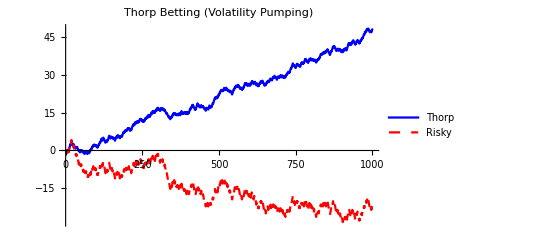

```mathematica
vvnSim=xSimThorp[{2,0.5},1000];
vnRebalanced=Log[FoldList[Times,1,vvnSim.{0.5,0.5}]];
vnRiskyOnly=Log[FoldList[Times,1,vvnSim.{0,1}]];
ListLinePlot[{vnRebalanced,vnRiskyOnly},
PlotStyle->{{ Blue},{Red,Dashed}},
PlotLabel->Style["Thorp Betting (Volatility Pumping)",FontSize->14],
PlotLegends->{"Thorp","Risky"}
]
```

Simulating 1,000 such cases clearly illustrates the effect of reducing volatility on return.

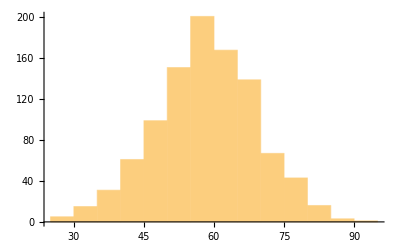

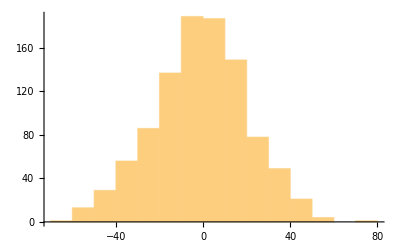

```mathematica
{vnThorp,vnRisky}=Transpose[
Table[
{Log[Fold[Times,1,#.{0.5,0.5}]],Log[Fold[Times,1,#⟦All,2⟧]]}&[xSimThorp[{2,0.5},1000]],
{1000}
]
];
Histogram[vnThorp]
Histogram[vnRisky]
```

## Optimal Continuous Time Growth

A multivariate geometric Brownian motion is described by the following equations

ⅆr_i(t)=(ⅆS_i(t))/(S_i(t))=μ_i ⅆt+σ_i ⅆW_i(t)

In addition, cross products of ⅆW(t) terms are scaled by their covariances

Cov[ⅆW_i(t) ⅆW_j(t)]=σ_(i,j)ⅆt

If we form a portfolio of N instruments with weights x = {x_1, x_2, x_3, ⃛, x_N}

(ⅆV(t))/(V(t))=∑_(i=1)^N x_i(ⅆS_i(t))/(S_i(t))=∑_(i=1)^N x_i(μ_i ⅆt+σ_i ⅆ W_i(t))

The variance of the stochastic term is

(E(∑_(i=1)^N x_i σ_i ⅆ W_i(t)))^2=∑_(i=1)^N ∑_(j=1)^N x_i x_j σ_(i,j)ⅆt

So V(t) is log normal with

E[log[(V(t))/(V(0))]]=(∑_(i=1)^N x_i μ_i -1/2∑_(i=1)^N ∑_(j=1)^N x_i x_j σ_(i,j))t

### Example - Understanding Volatility Pumping

Consider a collection of independent instruments with the same drift and volatility

ⅆr_i(t)=(ⅆS_i(t))/(S_i(t))=μ ⅆt+σⅆW_i(t)

The expected log return for each stock is μ – σ^2/2; however, if build an equally weighted portfolio Π of N such instruments, then

E[log[(Π(t))/(Π(t-1))]]=μ -1/2 σ^2/N

Growth is reduced by volatility, so by diversifying the portfolio, we realize a lower volatility and, hence, a higher rate of growth.

## Kelly Betting

The Kelly criterion or Kelly bet (https://en.wikipedia.org/wiki/Kelly_criterion) is a formula that leads to maximizing wealth in the long run by maximizing expected value of the logarithm of wealth. This is equivalent to maximizing the expected geometric growth rate.

For a simple example, consider a lottery in which you have a current wealth w, a probability of winning p, and the following pay-offs assuming you have decided to be bet 0≤b≤w.

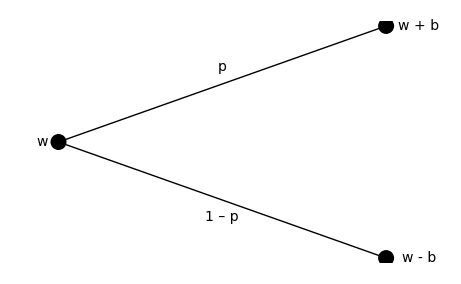

The optimal bet is to maximize the expected log wealth log[E[W_+]].

E[log[W_+]]= p log[w+b ]+(1+p)log[w-b]

Stated in terms of the current wealth w and the lottery parameter p

argmax_b[p log[w+b ]+(1+p)log[w-b]]

If 0<p≤0.5, then the solution can be found by solving for b in

solve_b[ⅆE[log[W_+]]/ⅆb==0]

```mathematica
FullSimplify@Solve[D[(p Log[w+b]+(1-p)Log[w-b]), b]==0,b]
```

{{b→(-1+2 p) w}}

The optimal bet is, therefore,

b=w(2p-1)

Thus, the optimal policy is to bet 2p-1 times your current wealth w.